Run the below cell to load the library and make sure the Graph outputs are formatted nicely

#### Importing library

```mathematica
Import[NotebookDirectory[]<>"library_graphStates.m"]
```

```mathematica
style={VertexShapeFunction->"Circle",VertexStyle->Directive[EdgeForm[{Thickness[0.01],Black}],LightGray],EdgeStyle->Directive[Black,Thickness[0.01]],VertexLabels->Placed["Name",{1/2,1/2}],VertexLabelStyle->Directive[Black,FontFamily->"IBM Plex Mono",25],VertexSize->0.4,GraphLayout->"CircularEmbedding"};
```

# Graph exploring

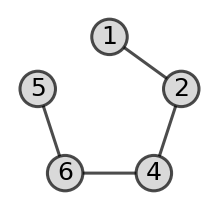

```mathematica
(* indexing the graphs based on their order of appearence *)
```

```mathematica
(* The LU family of graphs where qubits 4 and 3 represent charlie and debbie *)
```

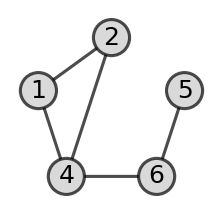
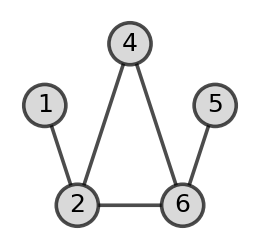
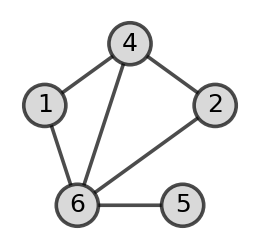
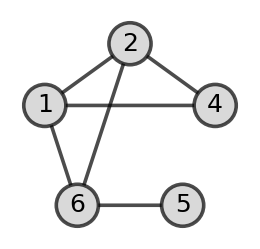
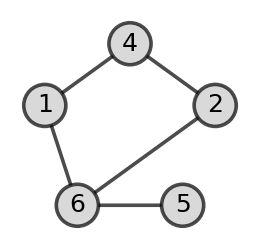
```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

## Graph 1

#### Z measurements

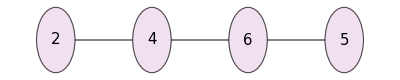

```mathematica
Zmeasurement[-Graphics-,1]
```

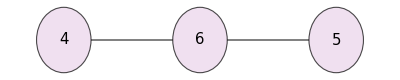

```mathematica
Zmeasurement[-Graphics-,2]
```

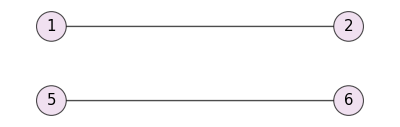

```mathematica
Zmeasurement[-Graphics-,4]
```

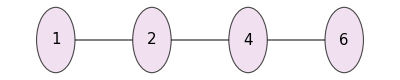

```mathematica
Zmeasurement[-Graphics-,5]
```

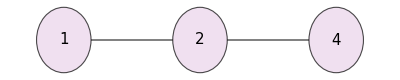

```mathematica
Zmeasurement[-Graphics-,6]
```

#### X measurements

```mathematica
Xmeasurement[-Graphics-,1]
```

AdjacencyList::inv: The argument 2 in AdjacencyList[Graph[<3>, <2>], 2] is not a valid vertex.

-Graphics-

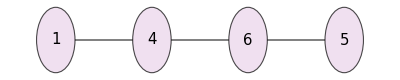

```mathematica
Xmeasurement[-Graphics-,2]
```

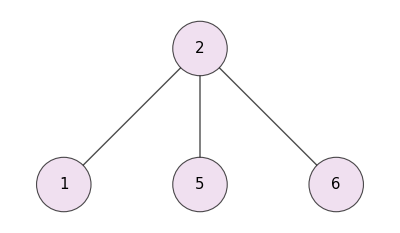

```mathematica
Xmeasurement[-Graphics-,4]
```

```mathematica
Xmeasurement[-Graphics-,5]
```

AdjacencyList::inv: The argument 6 in AdjacencyList[Graph[<3>, <2>], 6] is not a valid vertex.

-Graphics-

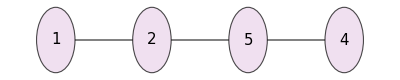

```mathematica
Xmeasurement[-Graphics-,6]
```

### Graph 1 to GHZ state

```mathematica
Xmeasurement[-Graphics-,4]
```

-Graphics-

#### Operation possibility 1 with target 4

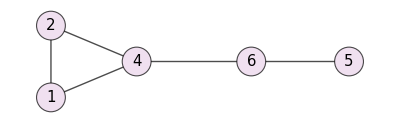

```mathematica
FindLUequivalent[-Graphics-,2]
```

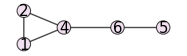
```mathematica
Ymeasurement[-Graphics-,4]
```

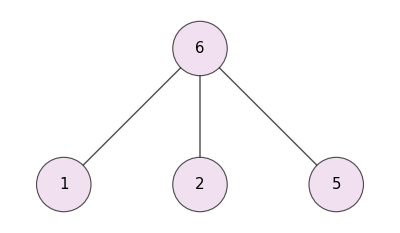

```mathematica
~
```

#### Operation possibility 2 with target 4

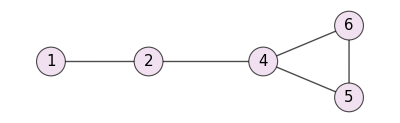

```mathematica
FindLUequivalent[-Graphics-,6]
```

```mathematica
Ymeasurement[-Graphics-,4]
```

-Graphics-

## Graph 2

#### Z measurements

```mathematica
Zmeasurement[-Graphics-,1]
```

-Graphics-

```mathematica
Zmeasurement[-Graphics-,2]
```

-Graphics-

```mathematica
Zmeasurement[-Graphics-,4]
```

-Graphics-

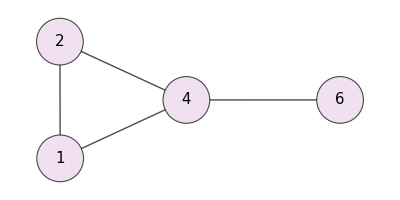

```mathematica
Zmeasurement[-Graphics-,5]
```

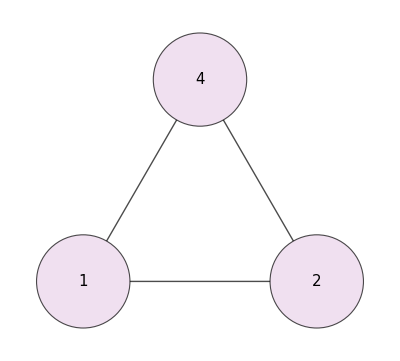

```mathematica
Zmeasurement[-Graphics-,6]
```

#### Y measurements

```mathematica
Ymeasurement[-Graphics-,1]
```

-Graphics-

```mathematica
Ymeasurement[-Graphics-,2]
```

-Graphics-

```mathematica
Ymeasurement[-Graphics-,4]
```

-Graphics-

```mathematica
Ymeasurement[-Graphics-,5]
```

-Graphics-

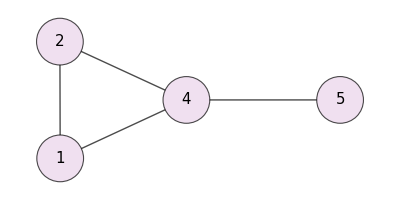

```mathematica
Ymeasurement[-Graphics-,6]
```

```mathematica
Zmeasurement
```

## Graph 4

### Z measurements

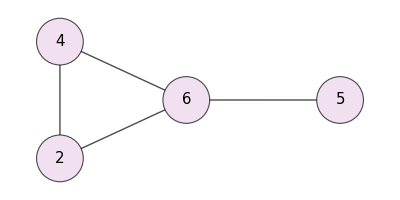

```mathematica
Zmeasurement[-Graphics-,1]
```

```mathematica
Zmeasurement[-Graphics-,2]
```

-Graphics-

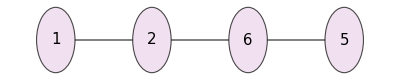

```mathematica
Zmeasurement[-Graphics-,4]
```

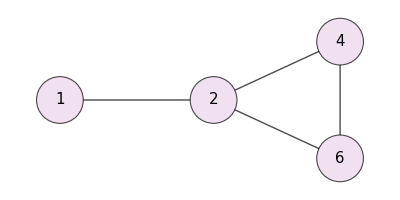

```mathematica
Zmeasurement[-Graphics-,5]
```

```mathematica
Zmeasurement[-Graphics-,6]
```

-Graphics-

### Y measurements

```mathematica
Ymeasurement[-Graphics-,1]
```

-Graphics-

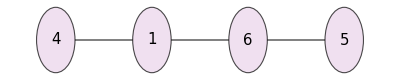

```mathematica
Ymeasurement[-Graphics-,2]
```

```mathematica
Ymeasurement[-Graphics-,4]
```

-Graphics-

```mathematica
Ymeasurement[-Graphics-,5]
```

-Graphics-

```mathematica
Ymeasurement[-Graphics-,6]
```

-Graphics-

#### To a Bell state

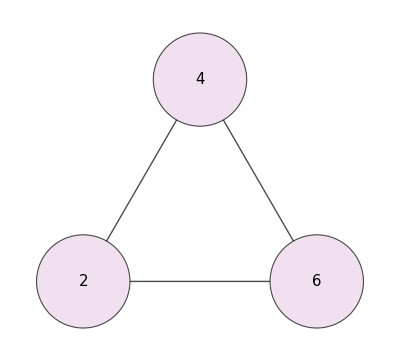

```mathematica
Zmeasurement[-Graphics-,5]
```

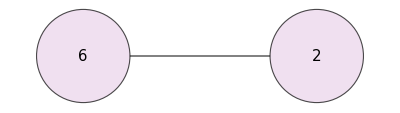

```mathematica
Zmeasurement[-Graphics-,4]
```

## Graph 5

#### Z measurements

```mathematica
Zmeasurement[-Graphics-,1]
```

-Graphics-

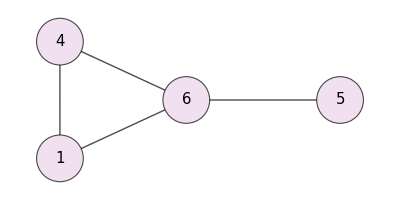

```mathematica
Zmeasurement[-Graphics-,2]
```

```mathematica
Zmeasurement[-Graphics-,4]
```

-Graphics-

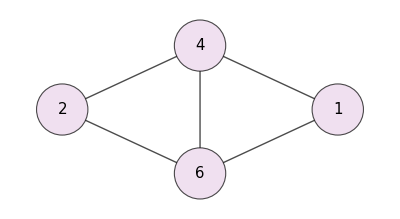

```mathematica
Zmeasurement[-Graphics-,5]
```

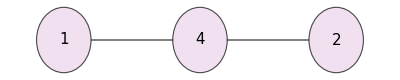

```mathematica
Zmeasurement[-Graphics-,6]
```

#### Y measurements

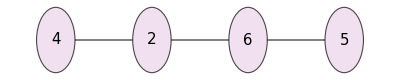

```mathematica
Ymeasurement[-Graphics-,1]
```

```mathematica
Ymeasurement[-Graphics-,2]
```

-Graphics-

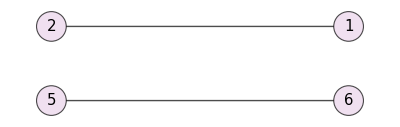

```mathematica
Ymeasurement[-Graphics-,4]
```

```mathematica
Ymeasurement[-Graphics-,5]
```

-Graphics-

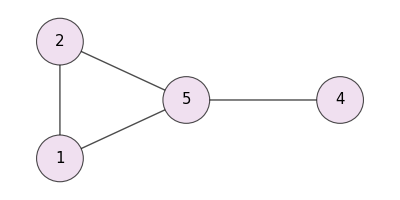

```mathematica
Ymeasurement[-Graphics-,6]
```